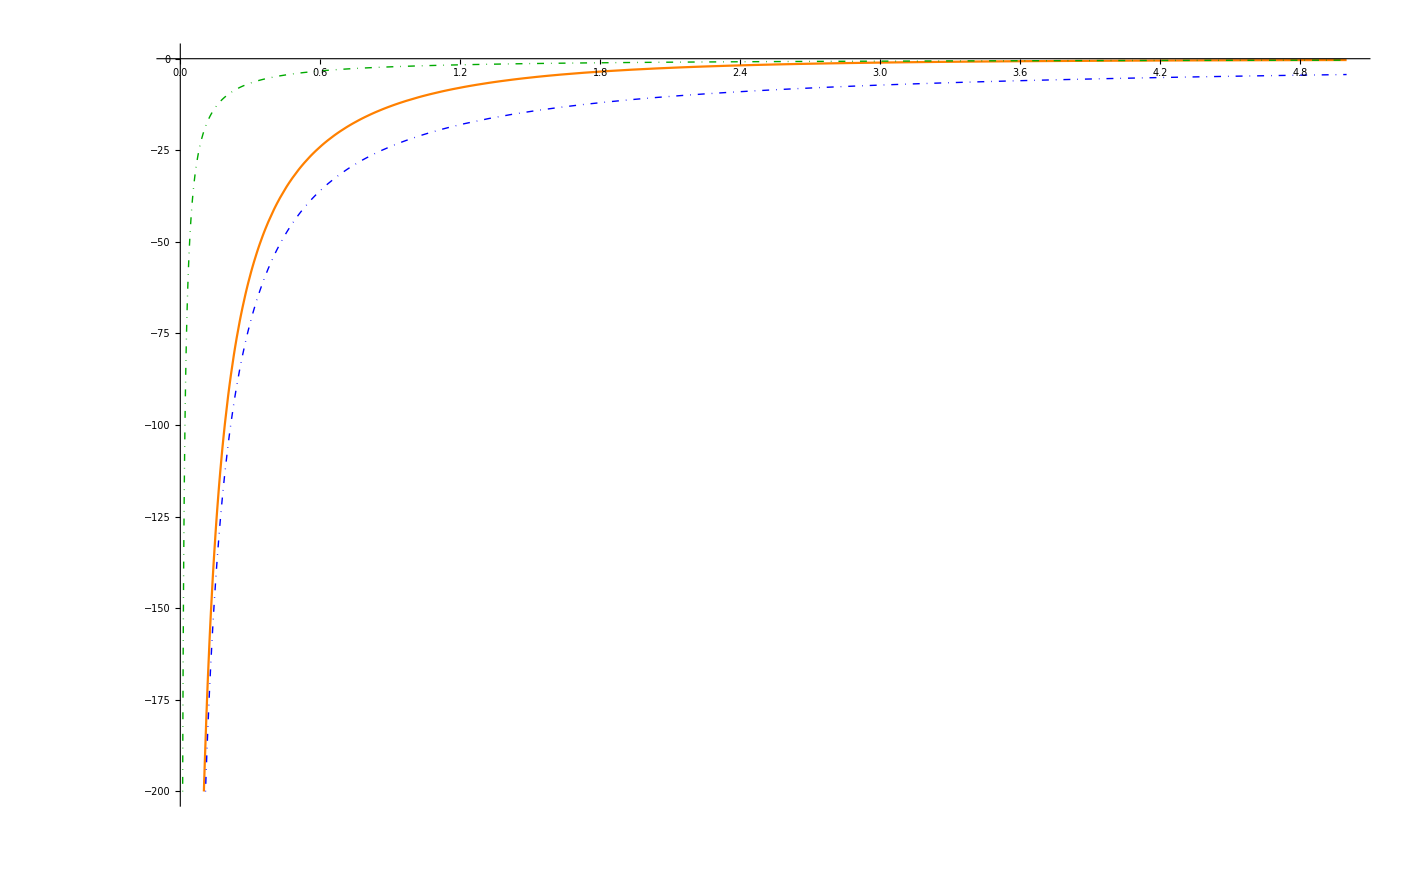

```mathematica
Block[{
𝓀,rules,rule
},
rules={
{η->11.4,A->1.1750,γ0->0.7572,γ1->0.3223,γ2->2.044},
{η->10.8,A->1.1750,γ0->0.7572,γ1->0.3223,γ2->2.044},
{η->11.3,A->1.000,γ0->0.9500,γ1->0.0000,γ2->2.044},
{η->10.8,A->0.8918,γ0->0.9743,γ1->0.1586,γ2->0.1586}
};
rule=rules[[2]];
𝓀[r_]=1+A η Exp[-γ0 r]+(1-A)η Exp[-γ1 r]-Exp[-γ2 r]/.rule;
Plot[{Style[-2/r 𝓀[r],Orange],Style[-2/r,DotDashed,Thickness[Medium],Darker[Green]],Style[-2/r 𝓀[0],DotDashed,Thickness[Medium],Blue]},{r,0,5},PlotRange->{-200,0}]
]
```

```mathematica
Block[{𝓀,rules},
rules={
{η->11.4,A->1.1750,γ0->0.7572,γ1->0.3223,γ2->2.044},
{η->10.8,A->1.1750,γ0->0.7572,γ1->0.3223,γ2->2.044},
{η->11.3,A->1.000,γ0->0.9500,γ1->0.0000,γ2->2.044},
{η->10.8,A->0.8918,γ0->0.9743,γ1->0.1586,γ2->0.1586}
};
Do[
𝓀[r_]:=1+A η Exp[-γ0 r]+(1-A)η Exp[-γ1 r]-Exp[-γ2 r]/.rules[[n]];
Table[Derivative[m][𝓀][0],{m,0,5}]//Print;
,{n,1,4}]
]
```

{11.4,-7.45571,3.29488,2.79116,-13.0733,32.351}

{10.8,-6.95572,2.90157,3.09372,-13.3039,32.5262}

{11.3,-8.691,6.02031,-1.14864,-8.25123,26.9346}

{10.8,-9.41065,9.14699,-8.90845,8.67895,-8.45582}